(a ⅇ^(-b r))/(b r)

(a1 ⅇ^(-b1 r))/(b1 r)+(a2 ⅇ^(-b2 r))/(b2 r)

(a1 ⅇ^(-b1 r))/(b1 r)+(a2 ⅇ^(-b2 r))/(b2 r)+(a3 ⅇ^(-b3 r))/(b3 r)

4631

-1787

-7.847

4

2.5

0.7072

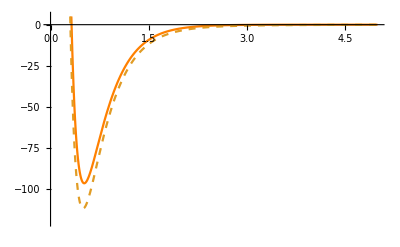

```mathematica
y[r_,a_,b_] = a Exp[-b r]/(b r)
m2y[r_,a1_,a2_,b1_,b2_] = y[r,a1,b1]+y[r,a2,b2]
m3y[r_,a1_,a2_,a3_,b1_,b2_,b3_] = y[r,a1,b1]+y[r,a2,b2]+y[r,a3,b3]
(* Reid *)
alp1 = 4631
alp2=-1787
alp3=-7.847
bet1 = 4
bet2=2.5
bet3=0.7072

p1=Plot[{m2y[r,alp1,alp2,bet1,bet2],m3y[r,alp1,alp2,alp3,bet1,bet2,bet3]},{r,0,5},PlotRange->{{0,5},{-120,5}},PlotStyle->{Orange,Dashed}]
```